Computes the Natural Frequencies of a (Micro/Nano-)Beam-Mass Structure.

```mathematica
Remove["Global`*"];
```

```mathematica
ΦEqn= ω^2 Φ[x]== Derivative[4][Φ][x];
ΦBC={Φ[0]==0,Φ'[0]==0,Φ''[1]==0,Derivative[3][Φ][1]==-M ω^2 Φ[1]};
```

```mathematica
ΦSol[x_]=Collect[DSolve[ΦEqn,Φ,x][[1,1,2]][x]//ExpToTrig,{Sin[arg_],Cos[arg_],Sinh[arg_],Cosh[arg_]}]/.{C[1]->H1,C[2]+C[4]->H3,C[3]->H2,-C[2]+C[4]->H4};
```

```mathematica
ΦCoef=Flatten[Solve[({ΦBC[[1]],ΦBC[[2]],ΦBC[[3]]}/.{Φ->ΦSol}//Expand//Chop),{H1,H2,H3}]];
```

```mathematica
ΦCharEq=Collect[(ΦBC[[4]]/.{Φ->ΦSol}/.ΦCoef//Expand),H4]/.H4->1
```

ω^(3/2) Cos[√ω]+ω^(3/2) Cosh[√ω]+(ω^(3/2) Sin[√ω]^2)/(Cos[√ω]+Cosh[√ω])-(ω^(3/2) Sinh[√ω]^2)/(Cos[√ω]+Cosh[√ω])==M ω^2 Sin[√ω]-(M ω^2 Cos[√ω] Sin[√ω])/(Cos[√ω]+Cosh[√ω])+(M ω^2 Cosh[√ω] Sin[√ω])/(Cos[√ω]+Cosh[√ω])-M ω^2 Sinh[√ω]-(M ω^2 Cos[√ω] Sinh[√ω])/(Cos[√ω]+Cosh[√ω])+(M ω^2 Cosh[√ω] Sinh[√ω])/(Cos[√ω]+Cosh[√ω])

```mathematica
inputData:={da->10×10^-6,db->10×10^-6,dL->400×10^-6,dgv->2×10^-6,dgw->2×10^-6,ρ->2300,dE->169×10^9,dm->2330×(10×10^-6×10×10^-6),dAv->1000×10^-12,dAw->1000×10^-12,dM->2330×(10×(200×100))×10^-18};ndRule:={ℓ->dL,a0->db,g0->dgv,dI->1/12×da×db^3,dJ->Integrate[ρ×y^2,{y,-da/2, da/2},{z,-db/2, db/2}]};
ndData:={τ->Sqrt[(dE dI)/(dm ℓ^4)],M->dM/(dm ℓ),J->dJ/(dm ℓ^2) }/.ndRule/.inputData//Chop
```

```mathematica
vωn=((FindRoot[(ΦCharEq//.ndData),{ω,#}][[1,2]]&/@{1,15,50}))//Chop
```

{0.756937,15.6023,50.1623}

```mathematica
ΦFreqEq[ω]=((ΦCharEq//.ndData))[[1]]-((ΦCharEq//.ndData))[[2]]
```

ω^(3/2) Cos[√ω]+ω^(3/2) Cosh[√ω]-5 ω^2 Sin[√ω]+(5 ω^2 Cos[√ω] Sin[√ω])/(Cos[√ω]+Cosh[√ω])-(5 ω^2 Cosh[√ω] Sin[√ω])/(Cos[√ω]+Cosh[√ω])+(ω^(3/2) Sin[√ω]^2)/(Cos[√ω]+Cosh[√ω])+5 ω^2 Sinh[√ω]+(5 ω^2 Cos[√ω] Sinh[√ω])/(Cos[√ω]+Cosh[√ω])-(5 ω^2 Cosh[√ω] Sinh[√ω])/(Cos[√ω]+Cosh[√ω])-(ω^(3/2) Sinh[√ω]^2)/(Cos[√ω]+Cosh[√ω])

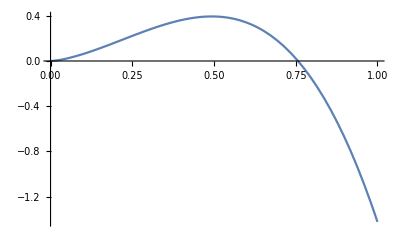

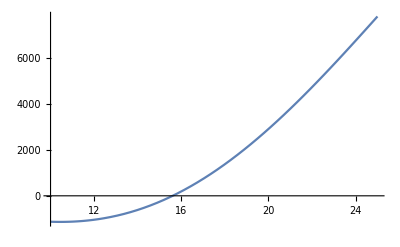

```mathematica
Plot[Evaluate[ΦFreqEq[ω]],{ω,0,1}]
Plot[Evaluate[ΦFreqEq[ω]],{ω,10,25}]
```

References:
S. Amir Mousavi Lajimi and Heppler,  Comments on “Natural frequencies of a uniform cantilever with a tip mass slender in the axial direction”, Journal of Sound and Vibration, Vol. 331, No. 2,  pp. 2964-2968, 2012.